```mathematica
description="Intermediate calculations";
$LoadAddOns={"FeynArts", "FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)";
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
MakeBoxes[m0, TraditionalForm] := "\!\(\*SubscriptBox[\(m\),\(0\)]\)";
MakeBoxes[m1, TraditionalForm] := "\!\(\*SubscriptBox[\(m\),\(1\)]\)";
MakeBoxes[m2, TraditionalForm] := "\!\(\*SubscriptBox[\(m\),\(2\)]\)";
MakeBoxes[mV, TraditionalForm] := "\!\(\*SubscriptBox[\(m\),\(V\)]\)";
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[λz,TraditionalForm]:=SubscriptBox["λ","z"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[Cfinite,TraditionalForm]:=SubscriptBox["C","finite"];
```

## Isolated slepton-side diagram

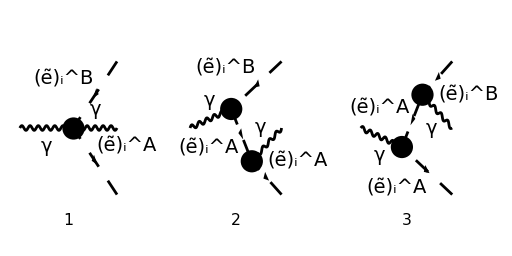

```mathematica
diags=InsertFields[
CreateTopologies[0,1->3],
{V[1]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags,
ColumnsXRows->{3,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{q},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
List->True,
DropSumOver->True,
SMP->True
]
```

{2 e^2 g^Lor1Lor2 (ε^*)^Lor2(k) ε^Lor1(q) IndexDelta(A,B),(e^2 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2),(e^2 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(A,2,i))^2)}

```mathematica
M[0]=Total[Mlist]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1,D],MSf[A,2,i]]]->FeynAmpDenominator[PropagatorDenominator[Momentum[k+k1,D],MSf[B,2,i]]]} (*FeynCalc chooses to use A-mass in both propagators, so we manually change the one corresponding with radiation from slepton B to a B-mass, although they are equal due to Kronecker delta *)
```

(e^2 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+(e^2 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+2 e^2 g^Lor1Lor2 (ε^*)^Lor2(k) ε^Lor1(q) IndexDelta(A,B)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
```

```mathematica
M[1]=M[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]}
```

(e^2 q^Lor1 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+(e^2 q^Lor1 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+2 e^2 q^Lor1 g^Lor1Lor2 (ε^*)^Lor2(k) IndexDelta(A,B)

```mathematica
M[2]=M[1]//Contract//FeynAmpDenominatorExplicit
```

2 e^2 IndexDelta(A,B) (q·ε^*(k))+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (k·q+k_1·q-k_2·q))/(2 (k·k_1)+k^2)+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (k·q-k_1·q+k_2·q))/(2 (k·k_2)+k^2)

```mathematica
M[3]=M[2]/.{Momentum[q,D]->Momentum[k1+k2+k,D]}
```

(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_1·ε^*(k))) (k·(k+k_1+k_2)+k_1·(k+k_1+k_2)-k_2·(k+k_1+k_2)))/(2 (k·k_1)+k^2)+(e^2 IndexDelta(A,B) (-(k·ε^*(k))-2 (k_2·ε^*(k))) (k·(k+k_1+k_2)-k_1·(k+k_1+k_2)+k_2·(k+k_1+k_2)))/(2 (k·k_2)+k^2)+2 e^2 IndexDelta(A,B) ((k+k_1+k_2)·ε^*(k))

```mathematica
M[4]=M[3]//ExpandScalarProduct//Simplify
```

(2 e^2 IndexDelta(A,B) ((MSf(A,2,i))^2-(MSf(B,2,i))^2) ((k·k_2) (k·ε^*(k)+2 (k_1·ε^*(k)))+k^2 (k_1·ε^*(k)-k_2·ε^*(k))-(k·k_1) (k·ε^*(k)+2 (k_2·ε^*(k)))))/((2 (k·k_1)+k^2) (2 (k·k_2)+k^2))

```mathematica
M[5]=M[4]/.{B->A} (*Can do this for photon case since IndexDelta*)
```

0

### Doing 4-point diagram separately

#### Radiation from sleptons

```mathematica
M23[0]=Total[Mlist[[{2,3}]]]
```

(e^2 (ε^*)^Lor2(k) (-k-2 k_1)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(A,2,i))^2)+(e^2 (ε^*)^Lor2(k) (-k-2 k_2)^Lor2 ε^Lor1(q) IndexDelta(A,B) (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
M23[1]=M23[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]};
M23[2]=M23[1]//Contract//FeynAmpDenominatorExplicit;
M23[3]=M23[2]/.{Momentum[q,D]->Momentum[k1+k2+k,D]};
M23[4]=M23[3]//ExpandScalarProduct//Simplify
```

e^2 IndexDelta(A,B) (-((k·ε^*(k)+2 (k_2·ε^*(k))) ((MSf(A,2,i))^2-(MSf(B,2,i))^2+2 (k·k_2)+k^2))/(2 (k·k_2)+k^2)-(k·ε^*(k))-2 (k_1·ε^*(k)))

```mathematica
M23[5]=M23[4]/.{B->A}
```

e^2 (-2 (k·ε^*(k))-2 (k_1·ε^*(k))-2 (k_2·ε^*(k)))

#### 4-point

```mathematica
M1[0]=Mlist[[1]]
```

2 e^2 g^Lor1Lor2 (ε^*)^Lor2(k) ε^Lor1(q) IndexDelta(A,B)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2;
SPD[k2]=MSf[A,2,i]^2;
M1[1]=M1[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]};
M1[2]=M1[1]//Contract//FeynAmpDenominatorExplicit;
M1[3]=M1[2]/.{Momentum[q,D]->Momentum[k1+k2+k,D]};
M1[4]=M1[3]//ExpandScalarProduct//Simplify
```

2 e^2 IndexDelta(A,B) (k·ε^*(k)+k_1·ε^*(k)+k_2·ε^*(k))

```mathematica
M1[5]=M1[4]/.{B->A}
```

2 e^2 (k·ε^*(k)+k_1·ε^*(k)+k_2·ε^*(k))

#### Combining them

```mathematica
Mtot[0]=M1[5]+M23[5]//Simplify
```

0

Thus we see that we must include the 4-point diagram for the Ward identity to hold!

### With Z-boson instead

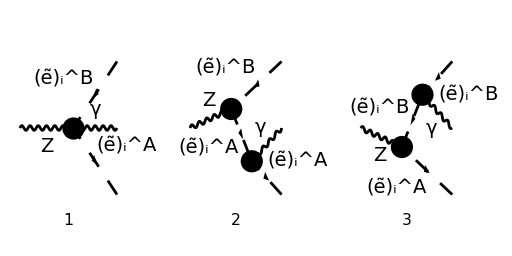

```mathematica
diags=InsertFields[
CreateTopologies[0,1->3],
{V[2]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes}
];
Paint[
diags,
ColumnsXRows->{3,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags],
IncomingMomenta->{q},
OutgoingMomenta->{k1,k,k2},
ChangeDimension->D,
UndoChiralSplittings->True,
List->False,
DropSumOver->True,
SMP->True
]//Simplify
```

-1/(2 (cos(θ_W)) (sin(θ_W)))e^2 (ε^*)^Lor2(k) ε^Lor1(q) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2)

```mathematica
FCClearScalarProducts[];
SPD[k1]=MSf[B,2,i]^2; (*Yes, both are m_A since Kronecker delta*)
SPD[k2]=MSf[A,2,i]^2;
M[1]=M[0]/.{Momentum[Polarization[q,I],D]->Momentum[q,D]}
```

-1/(2 (cos(θ_W)) (sin(θ_W)))e^2 q^Lor1 (ε^*)^Lor2(k) (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2)

```mathematica
M[2]=M[1]/.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify
```

-1/(2 (cos(θ_W)) (sin(θ_W)))e^2 q^Lor1 (ε^*)^Lor2(k) (2 (sin(θ_W))^2 A,B-USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2)

```mathematica
M[3]=M[2]/.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

(e^2 ZliAB q^Lor1 (ε^*)^Lor2(k) (((-k-2 k_2)^Lor2 (k-k_1+k_2)^Lor1)/((k+k_2)^2-(MSf(A,2,i))^2)+((-k-2 k_1)^Lor2 (k+k_1-k_2)^Lor1)/((k+k_1)^2-(MSf(B,2,i))^2)+2 g^Lor1Lor2))/((cos(θ_W)) (sin(θ_W)))

```mathematica
M[4]=M[3]//Contract//FeynAmpDenominatorExplicit;
M[5]=M[4]/.{Momentum[q,D]->Momentum[k1+k2+k,D]};
M[6]=M[5]//ExpandScalarProduct;
M[7]=M[6]//Simplify
```

(2 e^2 ZliAB ((MSf(A,2,i))^2-(MSf(B,2,i))^2) ((k·k_2) (k·ε^*(k)+2 (k_1·ε^*(k)))+k^2 (k_1·ε^*(k)-k_2·ε^*(k))-(k·k_1) (k·ε^*(k)+2 (k_2·ε^*(k)))))/((cos(θ_W)) (2 (k·k_1)+k^2) (2 (k·k_2)+k^2) (sin(θ_W)))

Using (4.3) in Tore, and including only the case where A,B not equal since the expression is zero otherwise, we get:

```mathematica
M[8]=M[7]/.{ZliAB->1/2 Cos[θil] Sin[θil]}
```

(e^2 sin(θil) cos(θil) ((MSf(A,2,i))^2-(MSf(B,2,i))^2) ((k·k_2) (k·ε^*(k)+2 (k_1·ε^*(k)))+k^2 (k_1·ε^*(k)-k_2·ε^*(k))-(k·k_1) (k·ε^*(k)+2 (k_2·ε^*(k)))))/((cos(θ_W)) (2 (k·k_1)+k^2) (2 (k·k_2)+k^2) (sin(θ_W)))

## Computing

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[k1, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(1\)]\)"; 
MakeBoxes[k2, TraditionalForm] := "\!\(\*SubscriptBox[\(k\),\(2\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\),\(1\)]\)";
MakeBoxes[m2,TraditionalForm]:="\!\(\*SubscriptBox[\(m\),\(2\)]\)";
```

```mathematica
p1l[l_]=Pair[Momentum[p1,D],LorentzIndex[l,D]];
p2l[l_]=Pair[Momentum[p2,D],LorentzIndex[l,D]];
```

```mathematica
k1l[lor_]=Pair[Momentum[k1,D],LorentzIndex[lor,D]];
k2l[lor_]=Pair[Momentum[k2,D],LorentzIndex[lor,D]];
kl[lor_]=Pair[Momentum[k,D],LorentzIndex[lor,D]];
```

```mathematica
K[lor1_,lor2_]=1/(SPD[k2,k])k1l[lor1] k2l[lor2]+1/SPD[k1,k] k1l[lor2] k2l[lor1]+MTD[lor1,lor2];
```

```mathematica
L[l1_,l2_]=K[l1,ρ] K[l2,ρ]//Contract;
L[μ,ν]
```

```mathematica
H[l1_,l2_]=2 p1l[l1] p2l[l2]+2 p2l[l1] p1l[l2] - s MTD[l1,l2];
H[μ,ν]
```

```mathematica
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[p1,p2]=s/2;
```

```mathematica
HL[0]=H[μ,ν]L[μ,ν]//Contract//Simplify
```

### Compare with hand calculation

```mathematica
HLbyHand=SPD[k2]/SPD[k2,k]^2 (4 SPD[p1,k1] SPD[p2,k1]-s SPD[k1])+SPD[k1]/SPD[k1,k]^2 (4 SPD[p1,k2] SPD[p2,k2]-s SPD[k2]) + (2-D) s + (SPD[k1,k2]/(SPD[k1,k] SPD[k2,k])+1/SPD[k1,k]+1/SPD[k2,k]) (4 SPD[p1,k1] SPD[p2,k2] + 4 SPD[p1,k2] SPD[p2,k1] - 2 s SPD[k1,k2])
```

```mathematica
FCCompareResults[HL[0],HLbyHand];
```

### Simplify HL

```mathematica
FCClearScalarProducts[];
HL[1]=HL[0]/.{s->SPD[p1+p2]}//ExpandScalarProduct//Simplify
```

```mathematica
SetMandelstam[x,{p1,p2,-k1,-k2,-k},{0,0,m1,m2,0}];
HL[2]=HL[1]//Simplify
```

```mathematica
MandelstamRules={
x[2,4]->x[3,5]-x[1,2]+m2^2-x[1,4],
x[4,5]->x[1,2]+m1^2+m2^2-x[3,5]-x[3,4],
x[2,3]->2m1^2+m2^2-x[3,5]-x[1,3]-x[3,4]
}
```

```mathematica
HL[3]=HL[2]//.MandelstamRules//Simplify
```

```mathematica
HL[4]=HL[3]/.{
x[1,2]->s,
x[3,4]->Q^2
}//Simplify
```

```mathematica
P[μ_,ν_]=FVD[p1,μ]FVD[p2,ν]+FVD[p2,μ]FVD[p1,ν]
```

p_1^ν p_2^μ+p_1^μ p_2^ν

```mathematica
K[μ_,ν_]=SPD[k2]/SPD[k2,k]^2 FVD[k1,μ]FVD[k1,ν]+SPD[k1]/SPD[k1,k]^2 FVD[k2,μ]FVD[k2,ν]+MTD[μ,ν]+(SPD[k1,k2]/(SPD[k1,k]SPD[k2,k])+1/SPD[k1,k]+1/SPD[k2,k])(FVD[k1,μ]FVD[k2,ν]+FVD[k2,μ]FVD[k1,ν])
```

g^μν+(k_1^2 k_2^μ k_2^ν)/(k·k_1)^2+((k_1·k_2)/((k·k_1) (k·k_2))+1/(k·k_1)+1/(k·k_2)) (k_1^ν k_2^μ+k_1^μ k_2^ν)+(k_2^2 k_1^μ k_1^ν)/(k·k_2)^2

```mathematica
FCClearScalarProducts[];
expr=P[μ,ν]K[μ,ν]//Contract//DiracSimplify//Simplify
```

2 ((k_2^2 (k_1·p_1) (k_1·p_2))/(k·k_2)^2+(k_1^2 (k_2·p_1) (k_2·p_2))/(k·k_1)^2+((k·k_1+k·k_2+k_1·k_2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)))/((k·k_1) (k·k_2))+p_1·p_2)

```mathematica
FCClearScalarProducts[];
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k]=0;
SPD[p1]=0;
SPD[p2]=0;
```

```mathematica
expr
```

2 ((m_1^2 (k_2·p_1) (k_2·p_2))/(k·k_1)^2+(m_2^2 (k_1·p_1) (k_1·p_2))/(k·k_2)^2+((k·k_1+k·k_2+k_1·k_2) ((k_1·p_2) (k_2·p_1)+(k_1·p_1) (k_2·p_2)))/((k·k_1) (k·k_2))+p_1·p_2)

```mathematica
Q[μ_,ν_]=FVD[q,μ]FVD[q,ν]-SPD[k1+k2+k]MTD[μ,ν]
```

q^μ q^ν-g^μν (k+k_1+k_2)^2

```mathematica
exprQ=Q[μ,ν]K[μ,ν]//Contract//Simplify
```

(2 (k·k_1)+2 (k·k_2)+2 (k_1·k_2)+m_1^2+m_2^2) (-(m_1^2 m_2^2)/(k·k_1)^2-(m_1^2 m_2^2)/(k·k_2)^2-D-(2 (k_1·k_2) (k·k_1+k·k_2+k_1·k_2))/((k·k_1) (k·k_2)))+(m_1^2 (k_2·q)^2)/(k·k_1)^2+(m_2^2 (k_1·q)^2)/(k·k_2)^2+(2 (k_1·q) (k_2·q) (k·k_1+k·k_2+k_1·k_2))/((k·k_1) (k·k_2))+q^2

```mathematica
exprQ/.{q->k1+k2+k}//ExpandScalarProduct//Simplify
```

(2 (k·k_1)+2 (k·k_2)+2 (k_1·k_2)+m_1^2+m_2^2) (-(m_1^2 m_2^2)/(k·k_1)^2-(m_1^2 m_2^2)/(k·k_2)^2-D-(2 (k_1·k_2) (k·k_1+k·k_2+k_1·k_2))/((k·k_1) (k·k_2)))+(m_1^2 (k·k_2+k_1·k_2+m_2^2)^2)/(k·k_1)^2+(m_2^2 (k·k_1+k_1·k_2+m_1^2)^2)/(k·k_2)^2+(2 (k·k_1+k·k_2+k_1·k_2) (k·k_1+k_1·k_2+m_1^2) (k·k_2+k_1·k_2+m_2^2))/((k·k_1) (k·k_2))+2 (k·k_1)+2 (k·k_2)+2 (k_1·k_2)+m_1^2+m_2^2

```mathematica
FVD[q,μ]FVD[q,ν]K[μ,ν]//Contract//Simplify
```

(m_1^2 (k_2·q)^2)/(k·k_1)^2+(m_2^2 (k_1·q)^2)/(k·k_2)^2+(2 (k_1·q) (k_2·q) (k·k_1+k·k_2+k_1·k_2))/((k·k_1) (k·k_2))+q^2

## PV reduction of slepton-side counterterms

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(s-m1^2-m2^2);
SPD[q]=s;
SPD[q,r]=1/4(m2^2-m1^2);
```

V2

```mathematica
1/(I Pi^2)FVD[k-k1,ν]FAD[{k,m1},k+k1]
%//TID[#,k,ToPaVe->True]&//Simplify
```

-(ⅈ (k-k_1)^ν)/(π^2 (k^2-m_1^2).(k+k_1)^2)

(k_1^ν (A_0(m_1^2)-4 m_1^2 B_0(m_1^2,0,m_1^2)))/(2 m_1^2)

V3

```mathematica
1/(I Pi^2)FVD[k-k2,ν]FAD[{k,m2},k+k2]
%//TID[#,k,ToPaVe->True]&//Simplify
```

-(ⅈ (k-k_2)^ν)/(π^2 (k^2-m_2^2).(k+k_2)^2)

(k_2^ν (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2)))/(2 m_2^2)

V1

```mathematica
1/(I Pi^2)FVD[k+1/2 q,ν]SPD[k-k1,k+q+k2]FAD[{k,m1},k+k1,{k+k1+k2,m2}]
%//TID[#,k,ToPaVe->True]&//Simplify
%//ReplaceAll[#,{k1->1/2(q-r),k2->1/2(q+r)}]&//ExpandScalarProduct//Collect2[#,{
Pair[LorentzIndex[ν,D],Momentum[q,D]],
Pair[LorentzIndex[ν,D],Momentum[r,D]]
},IsolateNames->KK]&
```

-(ⅈ (k+q/2)^ν ((k-k_1)·(k+q+k_2)))/(π^2 (k^2-m_1^2).(k+k_1)^2.((k+k_1+k_2)^2-m_2^2))

(m_1^2 ((-((D-2) s B_0(m_1^2,0,m_1^2) (8 k_2^ν (3 m_1^2+m_2^2-s-2 (k_1·q)) m_1^2+2 k_1^ν (7 m_1^4+6 m_2^2 m_1^2-10 s m_1^2-4 (k_2·q) m_1^2+3 m_2^4+3 s^2-6 m_2^2 s-6 (m_1^2+m_2^2-s) (k_1·q))-q^ν (m_1^4-2 m_2^2 m_1^2-2 s m_1^2-4 (k_2·q) m_1^2+m_2^4+s^2-2 m_2^2 s-2 (m_1^2+m_2^2-s) (k_1·q))))-(D-2) s B_0(m_2^2,0,m_2^2) (-4 (m_1^2+m_2^2-s) k_2^ν (3 m_1^2+m_2^2-s-2 (k_1·q))-q^ν (4 (k_1·q) m_2^2+3 (m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)+2 (m_1^2+m_2^2-s) (k_2·q))+2 k_1^ν (3 m_1^4-18 m_2^2 m_1^2-6 s m_1^2-m_2^4+3 s^2-2 m_2^2 s+12 m_2^2 (k_1·q)+2 (m_1^2+m_2^2-s) (k_2·q)))-2 ((D-2) s (m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2) (2 k_1^ν-q^ν) (3 m_1^2+m_2^2-s-2 (k_1·q))+B_0(s,m_1^2,m_2^2) (s q^ν ((D-3) (m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2)-(D-2) (m_1^2-m_2^2-s) (k_1·q)-(D-2) (m_1^2-m_2^2+s) (k_2·q))+k_2^ν (-((D-2) (m_1^6+(5 s-3 m_2^2) m_1^4+3 (m_2^2-s)^2 m_1^2-(m_2^2-s)^2 (m_2^2+s)))+((D-2) m_1^4-2 ((D-2) m_2^2+(5-2 D) s) m_1^2+(m_2^2-s) ((D-2) m_2^2+(4-3 D) s)) (k_1·q)+((D-2) m_1^4+(2 (D-4) s-2 (D-2) m_2^2) m_1^2+(D-2) (m_2^2-s)^2) (k_2·q))+k_1^ν (-((D-2) (m_1^6+(5 s-3 m_2^2) m_1^4+3 (m_2^4-2 s m_2^2-3 s^2) m_1^2-m_2^6+3 s^3-3 m_2^2 s^2+m_2^4 s))+((D-2) m_1^4-2 (D-2) (m_2^2-2 s) m_1^2+(D-2) m_2^4-5 (D-2) s^2-4 (D-1) m_2^2 s) (k_1·q)+((D-2) m_1^4+(2 (D-3) s-2 (D-2) m_2^2) m_1^2+(m_2^2-s) ((D-2) m_2^2-D s)) (k_2·q))))) m_2^2+(D-2) A_0(m_2^2) (2 k_1^ν (m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s+(-m_1^2+m_2^2+s) (k_1·q)-(m_1^2-m_2^2+s) (k_2·q)) m_2^2+k_2^ν (2 m_2^6-4 m_1^2 m_2^4-7 s m_2^4+2 m_1^4 m_2^2+8 s^2 m_2^2+2 m_1^2 s m_2^2-2 (m_1^2-m_2^2+s) (k_1·q) m_2^2-3 s^3+6 m_1^2 s^2-3 m_1^4 s-2 (m_1^2 (m_2^2+s)-(m_2^2-s)^2) (k_2·q))))-(D-2) m_2^2 A_0(m_1^2) (2 k_2^ν (m_1^4-2 m_2^2 m_1^2-2 s m_1^2+m_2^4+s^2-2 m_2^2 s+(-m_1^2+m_2^2+s) (k_1·q)-(m_1^2-m_2^2+s) (k_2·q)) m_1^2+k_1^ν (2 m_1^6-4 m_2^2 m_1^4-5 s m_1^4+2 m_2^4 m_1^2+4 s^2 m_1^2-2 m_2^2 s m_1^2+2 (-m_1^2+m_2^2+s) (k_2·q) m_1^2-s^3+2 m_2^2 s^2-m_2^4 s-2 (m_1^4-(m_2^2+2 s) m_1^2+s (s-m_2^2)) (k_1·q))))/(4 (D-2) m_1^2 m_2^2 s (m_1^4-2 (m_2^2+s) m_1^2+(m_2^2-s)^2))

1/8 KK(7853) q^ν+1/8 KK(6906) r^ν

```mathematica
KK[6906]//FRH//FullSimplify//Collect2[#,{A0,B0,C0},Factoring->FullSimplify,IsolateNames->KK]&
```

KK(7870) B_0(s,m_1^2,m_2^2)+1/2 KK(7881) B_0(m_1^2,0,m_1^2)+1/2 KK(7877) B_0(m_2^2,0,m_2^2)+KK(7871) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)+1/4 KK(7883) A_0(m_1^2)+1/4 KK(7874) A_0(m_2^2)

```mathematica
KK[7881]//FRH
```

(m_1^2 (2 m_2^2-25 s)+3 (5 m_2^2-8 s) (m_2^2-s)-17 m_1^4)/(-2 m_1^2 (s+m_2^2)+(m_2^2-s)^2+m_1^4)

### PV reduction of slepton-side counterterms but with on-shell photon/Z-boson

```mathematica
$Assumptions={
m1∈PositiveReals,
m2∈PositiveReals,
mV∈PositiveReals
};
```

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1+k2]=SPD[q]=Q^2;
SPD[k1,k2]=1/2(SPD[k1+k2]-m1^2-m2^2);
SPD[K]=SPD[k2-k1]//ExpandScalarProduct;
SPD[q,K]=m2^2-m1^2;
```

#### V2

```mathematica
1/(I Pi^2)FVD[k-k1,ν]FAD[{k,m1},k+k1]
%//TID[#,k,ToPaVe->True]&//ReplaceAll[#,{
k1->1/2(q-K),
k2->1/2(q+K)
}]&//ExpandScalarProduct//FullSimplify
int2[0]=%//PaXEvaluateUVIRSplit//Collect2[#,{K,q},Factoring->(Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&)]&
```

-(ⅈ (k-k_1)^ν)/(π^2 (k^2-m_1^2).(k+k_1)^2)

-((K^ν-q^ν) (A_0(m_1^2)-4 m_1^2 B_0(m_1^2,0,m_1^2)))/(4 m_1^2)

K^ν (1/4 (3 log(μ^2)-6 log(m_1)-3 ℽ+7-3 log(π))+3/(4 ε_UV))+q^ν (1/4 (-3 log(μ^2)+6 log(m_1)+3 ℽ-7+3 log(π))-3/(4 ε_UV))

#### V3

```mathematica
1/(I Pi^2)FVD[k-k2,ν]FAD[{k,m2},k+k2]
%//TID[#,k,ToPaVe->True]&//ReplaceAll[#,{
k1->1/2(q-K),
k2->1/2(q+K)
}]&//ExpandScalarProduct//FullSimplify
int3[0]=%//PaXEvaluateUVIRSplit//Collect2[#,{K,q},Factoring->(Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&)]&
```

-(ⅈ (k-k_2)^ν)/(π^2 (k^2-m_2^2).(k+k_2)^2)

((K^ν+q^ν) (A_0(m_2^2)-4 m_2^2 B_0(m_2^2,0,m_2^2)))/(4 m_2^2)

K^ν (1/4 (-3 log(μ^2)+6 log(m_2)+3 ℽ-7+3 log(π))-3/(4 ε_UV))+q^ν (1/4 (-3 log(μ^2)+6 log(m_2)+3 ℽ-7+3 log(π))-3/(4 ε_UV))

#### V1

```mathematica
1/(I Pi^2)FVD[k,ν]SPD[k-k1,k+q+k2]FAD[{k,m1},k+k1,{k+k1+k2,m2}]
%//TID[#,k,ToPaVe->True]&//ReplaceAll[#,{
k1->1/2(q-K),
k2->1/2(q+K)
}]&//ExpandScalarProduct//FullSimplify
int1[0]=%//PaXEvaluateUVIRSplit//ExpandAll//Collect2[#,{K,q},Factoring->(Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Simplify,IsolateNames->KK]&)]&
```

-(ⅈ k^ν ((k-k_1)·(k+q+k_2)))/(π^2 (k^2-m_1^2).(k+k_1)^2.((k+k_1+k_2)^2-m_2^2))

1/(4 Q^2)((2 (2 Q^2 K^ν (-Q^2+m_1^2+m_2^2) (2 Q^2 B_0(Q^2,m_1^2,m_2^2)+(-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2) C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2))+q^ν ((-Q^2+m_1^2-m_2^2) (-Q^4+4 Q^2 m_1^2+(m_1^2-m_2^2)^2) B_0(Q^2,m_1^2,m_2^2)-2 Q^2 (-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2) (-Q^2+m_1^2+m_2^2) C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2))+Q^2 B_0(m_1^2,0,m_1^2) (-(K^ν (2 m_1^2 (Q^2+m_2^2)-3 (m_2^2-Q^2)^2+m_1^4))-q^ν (2 m_1^2 (3 m_2^2-5 Q^2)+3 (m_2^2-Q^2)^2+7 m_1^4))+Q^2 B_0(m_2^2,0,m_2^2) (K^ν (3 Q^4-2 Q^2 (3 m_1^2+m_2^2)+3 m_1^4-2 m_1^2 m_2^2-m_2^4)+q^ν (Q^4-2 Q^2 (m_1^2+3 m_2^2)+m_1^4+10 m_1^2 m_2^2+5 m_2^4))))/((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))-(A_0(m_2^2) (Q^2 K^ν+q^ν (Q^2-2 m_2^2)))/m_2^2-(Q^2 K^ν A_0(m_1^2))/m_1^2+(q^ν (Q^2-2 m_1^2) A_0(m_1^2))/m_1^2)

PaXEvaluate::C0D0: The explicit result for the occurring C0 function(s) is expected to be very complicated. Please rerun PaXEvaluate with the option PaXC0Expand->True to show the result nevertheless. Please set $FCAdvice=False if you do not want to see this message in future.

K^ν ((KK(6486))/ε_IR+(KK(6491))/4+1/(2 ε_UV))+q^ν (-(KK(6486))/ε_IR-(KK(6497))/4-1/(2 ε_UV))

#### Combining

```mathematica
int[0]=int1[0]+int2[0]+int3[0]//Collect2[#,{K,q},Factoring->(
Collect2[#,{EpsilonIR,EpsilonUV},Factoring->Simplify]&
)]&
```

K^ν ((KK(6486))/ε_IR+1/4 (KK(6491)-6 log(m_1)+6 log(m_2))+1/(2 ε_UV))+q^ν (-(KK(6486))/ε_IR+1/4 (-KK(6497)-6 log(μ^2)+6 log(m_1)+6 log(m_2)+6 ℽ-14+6 log(π))-2/ε_UV)

```mathematica
int[1]=int[0][[1]]
```

K^ν ((KK(6486))/ε_IR+1/4 (KK(6491)-6 log(m_1)+6 log(m_2))+1/(2 ε_UV))

```mathematica
int[2]=int[1]//FRH//ReplaceAll[#,{mV->0,FeynCalc`Collect`Private`unity->1}]&//FullSimplify
```

1/2 K^ν (2 (-Q^2+m_1^2+m_2^2) X`ScalarC0IR6(Q^2,m_1,m_2)+(2 (-Q^2+m_1^2+m_2^2) (log(2 m_1 m_2)-log(-Q^2+√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))+m_1^2+m_2^2)) (-ε_IR (log(-ⅈ μ)+log(ⅈ μ))+(ℽ-2) ε_IR+ε_IR log(π m_1 m_2)-1))/(ε_IR √((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2)))+log(-(ⅈ μ)/π)+log((ⅈ μ m_2^2)/m_1^4)+1/ε_UV-ℽ+3)

```mathematica
int[3]=int[2]//Collect2[#,K,Factoring->(Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&)]&
```

K^ν (1/2 (2 (-Q^2+m_1^2+m_2^2) X`ScalarC0IR6(Q^2,m_1,m_2)+log(-(ⅈ μ)/π)+(2 (-Q^2+m_1^2+m_2^2) (log(2 m_1 m_2)-log(-Q^2+√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))+m_1^2+m_2^2)) (-log(-ⅈ μ)-log(ⅈ μ)+log(π m_1 m_2)+ℽ-2))/(√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2)))+log((ⅈ μ m_2^2)/m_1^4)-ℽ+3)-((-Q^2+m_1^2+m_2^2) (log(2 m_1 m_2)-log(-Q^2+√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))+m_1^2+m_2^2)))/(ε_IR √((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2)))+1/(2 ε_UV))

```mathematica
intM[2]=int[1]//FRH//ReplaceAll[#,FeynCalc`Collect`Private`unity->1]&//Simplify//FullSimplify
```

1/2 K^ν (2 (-Q^2+m_1^2+m_2^2) X`ScalarC0IR6(Q^2,m_1,m_2)+(2 (-Q^2+m_1^2+m_2^2) (log(2 m_1 m_2)-log(-Q^2+√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))+m_1^2+m_2^2)) (-ε_IR (log(-ⅈ μ)+log(ⅈ μ))+(ℽ-2) ε_IR+ε_IR log(π m_1 m_2)-1))/(ε_IR √((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2)))+log(-(ⅈ μ)/π)+log((ⅈ μ m_2^2)/m_1^4)+1/ε_UV-ℽ+3)

```mathematica
intM[3]=intM[2]//Collect2[#,K,Factoring->(Collect2[#,{EpsilonIR,EpsilonUV},Factoring->FullSimplify]&)]&
```

K^ν (1/2 (2 (-Q^2+m_1^2+m_2^2) X`ScalarC0IR6(Q^2,m_1,m_2)+log(-(ⅈ μ)/π)+(2 (-Q^2+m_1^2+m_2^2) (log(2 m_1 m_2)-log(-Q^2+√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))+m_1^2+m_2^2)) (-log(-ⅈ μ)-log(ⅈ μ)+log(π m_1 m_2)+ℽ-2))/(√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2)))+log((ⅈ μ m_2^2)/m_1^4)-ℽ+3)-((-Q^2+m_1^2+m_2^2) (log(2 m_1 m_2)-log(-Q^2+√((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2))+m_1^2+m_2^2)))/(ε_IR √((-Q+m_1-m_2) (-Q+m_1+m_2) (Q+m_1-m_2) (Q+m_1+m_2)))+1/(2 ε_UV))

```mathematica
A0[m^2]//PaXEvaluateUVIRSplit
```

m^2/ε_UV-m^2 (-log(μ^2/(π m^2))+ℽ-1)

```mathematica
FAD[{k,m0},{k+p,m1}]//TID[#,k,ToPaVe->True]&
```

ⅈ π^2 B_0(p^2,m_0^2,m_1^2)

```mathematica
FAD[{k,m1},{k+p,m0}]//TID[#,k,ToPaVe->True]&
```

ⅈ π^2 B_0(p^2,m_0^2,m_1^2)

```mathematica
Integrate[Log[x],x]
```

x log(x)-x

## Origin of divergences: triangle or bubble?

```mathematica
$Assumptions={
s∈PositiveReals
};
```

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(s-m1^2-m2^2);
```

```mathematica
M23[0]=Prefac (A0[m1^2]/m1^2+A0[m2^2]/m2^2-4B0[m2^2,m2^2,0]-4B0[m1^2,m1^2,0])
M23IR[0]=M23[0]//PaXEvaluateIR//FullSimplify
M23UV[0]=M23[0]//PaXEvaluateUV//FullSimplify
```

Prefac (-4 B_0(m_1^2,0,m_1^2)-4 B_0(m_2^2,0,m_2^2)+(A_0(m_1^2))/m_1^2+(A_0(m_2^2))/m_2^2)

0

-(6 Prefac)/ε_UV

```mathematica
M1[0]=-2prefac(4SPD[k1,k2]C0[m1^2,m2^2,s,m1^2,0,m2^2]+2SPD[k1,k2]/(SPD[k1,k2]^2-m1^2m2^2)(s B0[s,m1^2,m2^2]-(m2^2+SPD[k1,k2])B0[m2^2,0,m2^2]-(m1^2+SPD[k1,k2])B0[m1^2,0,m1^2])+1/2(A0[m1^2]/m1^2+A0[m2^2]/m2^2)-B0[m2^2,0,m2^2]-B0[m1^2,0,m1^2])
M1IR[0]=M1[0]//PaXEvaluateIR//FullSimplify//ReplaceAll[#,{
m1->Sqrt[s]Sqrt[β1],
m2->Sqrt[s]Sqrt[β2],
-2m1^2(s+m2^2)+(m2^2-s)^2+m1^4->λ[s,m1^2,m2^2]
}]&//ReplaceAll[#,{
λ[s,m1^2,m2^2]->s^2λ[1,β1,β2]
}]&//Simplify
M1UV[0]=M1[0]//PaXEvaluateUV//FullSimplify
```

-2 prefac (((s-m_1^2-m_2^2) (-((1/2 (s-m_1^2-m_2^2)+m_1^2) B_0(m_1^2,0,m_1^2))-(1/2 (s-m_1^2-m_2^2)+m_2^2) B_0(m_2^2,0,m_2^2)+s B_0(s,m_1^2,m_2^2)))/(1/4 (s-m_1^2-m_2^2)^2-m_1^2 m_2^2)-B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)+2 (s-m_1^2-m_2^2) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)+1/2 ((A_0(m_1^2))/m_1^2+(A_0(m_2^2))/m_2^2))

(4 prefac (β1+β2-1) log((√(λ(1,β1,β2))+β1+β2-1)/(2 √β1 √β2)))/(ε_IR √(λ(1,β1,β2)))

(2 prefac)/ε_UV

prefac = MLO μ^(4-d) e^2/(32π^2)

```mathematica
M23IR[0]+M23UV[0]
M1IR[0]+M1UV[0]
```

-(6 Prefac)/ε_UV

(4 prefac (β1+β2-1) log((√(λ(1,β1,β2))+β1+β2-1)/(2 √β1 √β2)))/(ε_IR √(λ(1,β1,β2)))+(2 prefac)/ε_UV

σ = σLO  2 Re(Mvirt)

## Calculating loop integrals for counterterms (OLD)

Using q=k1+k2 and K=k2-k1 to extract only the parts proportional to k2-k1 (the ones that contribute to the counterterm).

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1+k2]=s;
SPD[k1,k2]=1/2(s-m1^2-m2^2);
```

```mathematica
I1μ=1/(I Pi^2)FVD[k,μ]SPD[k-k1,k+k1+2k2]FAD[{k,m1},k+k1,{k+k1+k2,m2}]//TID[#,k,ToPaVe->True]&//Simplify//FullSimplify//ReplaceAll[#,{
k1->1/2(q-K),
k2->1/2(q+K)
}]&//ExpandScalarProduct//Collect2[#,{q,K},Factoring->FullSimplify,IsolateNames->KK]&
I1=1/4KK[453]//FRH
```

1/4 KK(453) K^μ+1/4 KK(466) q^μ

1/4 (-((2 (-2 (-s+m_1^2+m_2^2) (2 s B_0(s,m_1^2,m_2^2)+((m_1-m_2)^2-s) ((m_1+m_2)^2-s) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2))+(-3 s^2+2 m_1^2 (3 s+m_2^2)+2 s m_2^2-3 m_1^4+m_2^4) B_0(m_2^2,0,m_2^2)+(2 m_1^2 (s+m_2^2)-3 (m_2^2-s)^2+m_1^4) B_0(m_1^2,0,m_1^2)))/(-2 m_1^2 (s+m_2^2)+(m_2^2-s)^2+m_1^4))-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2)

```mathematica
I2μ=1/(I Pi^2)FVD[k-k1,μ]FAD[{k,m1},k+k1]//TID[#,k,ToPaVe->True]&//Simplify//FullSimplify//ReplaceAll[#,{
k1->1/2(q-K),
k2->1/2(q+K)
}]&//ExpandScalarProduct//Collect2[#,{q,K},Factoring->FullSimplify,IsolateNames->KK]&
I2=KK[527]//FRH
```

KK(527) K^μ+KK(528) q^μ

B_0(m_1^2,0,m_1^2)-(A_0(m_1^2))/(4 m_1^2)

```mathematica
I3μ=1/(I Pi^2)FVD[k-k2,μ]FAD[{k,m2},k+k2]//TID[#,k,ToPaVe->True]&//Simplify//FullSimplify//ReplaceAll[#,{
k1->1/2(q-K),
k2->1/2(q+K)
}]&//ExpandScalarProduct//Collect2[#,{q,K},Factoring->FullSimplify,IsolateNames->KK]&
I3=KK[2393]//FRH
```

KK(2393) K^μ+KK(2393) q^μ

(A_0(m_2^2))/(4 m_2^2)-B_0(m_2^2,0,m_2^2)

```mathematica
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
```

```mathematica
mToβRules={
m1->Sqrt[s]Sqrt[β1],
m2->Sqrt[s]Sqrt[β2]
};
λRules={
-2m1^2(s+m2^2)+(m2^2-s)^2+m1^4->λs,
((m1-m2)^2-s)((m1+m2)^2-s)->λs,
2m1^2(s+m2^2)-3(m2^2-s)^2+m1^4->2m1^4-2(s-m2^2)^2-λs,
-3s^2+2m1^2(3s+m2^2)+2s m2^2-3m1^4+m2^4->-λs-2(s-m1^2)^2+2m2^4,
m1^4-2m2^2m1^2-2s m1^2+m2^4+s^2-2m2^2 s->λs
};
```

```mathematica
Ifull[0]=I1+I2+I3//FullSimplify//ReplaceAll[#,λRules]&
Ifull[1]=Ifull[0]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D),PaXC0Expand->True]&//ReplaceAll[#,λRules]&//FCHideEpsilon//Collect2[#,{SMP["Delta_UV"],SMP["Delta_IR"]},Factoring->FullSimplify,IsolateNames->KK]&
```

-1/(2 λ_s)(-2 (-s+m_1^2+m_2^2) (2 s B_0(s,m_1^2,m_2^2)+λ_s C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2))+B_0(m_2^2,0,m_2^2) (-λ_s-2 (s-m_1^2)^2+2 m_2^4)+B_0(m_1^2,0,m_1^2) (-λ_s-2 (s-m_2^2)^2+2 m_1^4))+B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)-(A_0(m_1^2))/(2 m_1^2)

KK(2478) Δ_IR+(KK(2494))/4+Δ_UV/2

```mathematica
KK[2478]//FRH
```

((-s+m_1^2+m_2^2) log((√λ_s-s+m_1^2+m_2^2)/(2 m_1 m_2)))/(√λ_s)

## Calculating loop diagrams for counterterms

```mathematica
$Assumptions={
s∈PositiveReals,
m1∈PositiveReals,
m2∈PositiveReals,
β1∈PositiveReals,
β2∈PositiveReals,
Q∈PositiveReals,
z∈PositiveReals,
EpsilonIR∈NegativeReals,(*Right?*)
EpsilonUV∈PositiveReals(*Right?*)
};
```

```mathematica
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2a b-2a c-2b c;
```

```mathematica
SPD[k1,q]=1/2(SPD[q]+SPD[k1]-SPD[k2]);
SPD[k2,q]=1/2(SPD[q]+SPD[k2]-SPD[k1]);
SPD[k1,k2]=1/2(SPD[q]-SPD[k1]-SPD[k2]);
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[q]=Q^2;
```

### Rules for changing to λ (Kallen function)

Also giving “proofs” of the rules. Can be seen by removing semicolons.

```mathematica
-2m1^2(m2^2+Q^2)+(m2^2-Q^2)^2+m1^4;
%+λQ-Kallen[Q^2,m1^2,m2^2]//FullSimplify;
```

```mathematica
-2m1^2(m2^2+3Q^2)-2m2^2Q^2+3m1^4-m2^4+3Q^4;
%+λQ-Kallen[Q^2,m1^2,m2^2]//FullSimplify;
```

```mathematica
2m1^2(m2^2+Q^2)-3(m2^2-Q^2)^2+m1^4;
%-λQ+Kallen[Q^2,m1^2,m2^2]//FullSimplify;
```

```mathematica
m1^4-2(m2^2+Q^2)m1^2+(m2^2-Q^2)^2;
%+λQ-Kallen[Q^2,m1^2,m2^2]//FullSimplify;
```

```mathematica
Q^4-2Q^2m1^2-2Q^2m2^2+m1^4-2m1^2m2^2+m2^4;
%+λQ-Kallen[Q^2,m1^2,m2^2];
```

```mathematica
(-Q+m1-m2)(-Q+m1+m2)(Q+m1-m2)(Q+m1+m2);
%+λQ-Kallen[Q^2,m1^2,m2^2]//FullSimplify;
```

```mathematica
λRules={
-2m1^2(m2^2+Q^2)+(m2^2-Q^2)^2+m1^4->λQ,
-2m1^2(m2^2+3Q^2)-2m2^2Q^2+3m1^4-m2^4+3Q^4->2(m1^2-Q^2)^2-2m2^4+λQ,
2m1^2(m2^2+Q^2)-3(m2^2-Q^2)^2+m1^4->-2(m2^2-Q^2)^2+2m1^4-λQ,
m1^4-2(m2^2+Q^2)m1^2+(m2^2-Q^2)^2->λQ,
Q^4-2Q^2m1^2-2Q^2m2^2+m1^4-2m1^2m2^2+m2^4->λQ,
(-Q+m1-m2)(-Q+m1+m2)(Q+m1-m2)(Q+m1+m2)->λQ
};
```

### Rules for changing from dimensional quantities (Q,m1,m2) to dimensionless quantities (z,β1,β2)

```mathematica
dimLessRules={
Q->Sqrt[s]Sqrt[z],
m1->Sqrt[s]Sqrt[β1],
m2->Sqrt[s]Sqrt[β2],
λQ->s^2λz
};
```

### Finding loops

#### Triangle diagram

```mathematica
I1[0]=1/(I Pi^2)(FVD[k,μ]+1/2FVD[q,μ])SPD[k-k1,k+q+k2]FAD[{k,m1},k+k1,{k+q,m2}]
I1[1]=%//TID[#,k,ToPaVe->True]&//Simplify//ReplaceAll[#,{k1->1/2(q-K),k2->1/2(q+K)}]&//ExpandScalarProduct//Simplify//Collect2[#,{Pair[LorentzIndex[μ,D],Momentum[q,D]],Pair[LorentzIndex[μ,D],Momentum[K,D]]},Factoring->FullSimplify,IsolateNames->KK]&//PaVeOrder
```

-(ⅈ (k^μ+q^μ/2) ((k-k_1)·(k+q+k_2)))/(π^2 (k^2-m_1^2).(k+k_1)^2.((k+q)^2-m_2^2))

1/4 (KK(1205) K^μ+KK(1222) q^μ)

```mathematica
I1[2]=1/4KK[1205]//FRH//ReplaceAll[#,{K->k2-k1}]&//ExpandScalarProduct//FullSimplify//ReplaceAll[#,λRules]&//FullSimplify
```

1/4 (1/λ_Q 2 (2 (-Q^2+m_1^2+m_2^2) (2 Q^2 B_0(Q^2,m_1^2,m_2^2)+λ_Q C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2))+B_0(m_2^2,0,m_2^2) (2 (m_1^2-Q^2)^2+λ_Q-2 m_2^4)+B_0(m_1^2,0,m_1^2) (2 (m_2^2-Q^2)^2+λ_Q-2 m_1^4))-(A_0(m_1^2))/m_1^2-(A_0(m_2^2))/m_2^2)

Make sure I have written it down correctly:

```mathematica
I1hand[2]=1/λQ(m1^2+m2^2-Q^2)(2Q^2B0[Q^2,m1^2,m2^2]+λQ C0[m1^2,m2^2,Q^2,m1^2,0,m2^2])-1/4(A0[m1^2]/m1^2+A0[m2^2]/m2^2)+1/(2λQ)((λQ+2(m2^2-Q^2)^2-2m1^4)B0[m1^2,0,m1^2]+(λQ+2(m1^2-Q^2)^2-2m2^4)B0[m2^2,0,m2^2])//FullSimplify;
FCCompareResults[{I1hand[2]},{I1[2]}]
```

Check of the results: The results agree.

True

#### Bubble diagrams

```mathematica
I2[0]=1/(I Pi^2)FVD[k-k1,μ]FAD[{k,m1},k+k1]
I2[1]=%//TID[#,k,ToPaVe->True]&//Simplify//ReplaceAll[#,{k1->1/2(q-K),k2->1/2(q+K)}]&//ExpandScalarProduct//Simplify//Collect2[#,{Pair[LorentzIndex[μ,D],Momentum[q,D]],Pair[LorentzIndex[μ,D],Momentum[K,D]]},Factoring->FullSimplify,IsolateNames->KK]&//PaVeOrder
```

-(ⅈ (k-k_1)^μ)/(π^2 (k^2-m_1^2).(k+k_1)^2)

KK(1285) K^μ+KK(1286) q^μ

```mathematica
I2[2]=KK[1285]//FRH
```

B_0(m_1^2,0,m_1^2)-(A_0(m_1^2))/(4 m_1^2)

```mathematica
I3[0]=1/(I Pi^2)FVD[k-k2,μ]FAD[{k,m2},k+k2]
I3[1]=%//TID[#,k,ToPaVe->True]&//Simplify//ReplaceAll[#,{k1->1/2(q-K),k2->1/2(q+K)}]&//ExpandScalarProduct//Simplify//Collect2[#,{Pair[LorentzIndex[μ,D],Momentum[q,D]],Pair[LorentzIndex[μ,D],Momentum[K,D]]},Factoring->FullSimplify,IsolateNames->KK]&//PaVeOrder
```

-(ⅈ (k-k_2)^μ)/(π^2 (k^2-m_2^2).(k+k_2)^2)

KK(1374) (K^μ+q^μ)

```mathematica
I3[2]=KK[1374]//FRH
```

(A_0(m_2^2))/(4 m_2^2)-B_0(m_2^2,0,m_2^2)

### Evaluating in PackageX

```mathematica
I1[3]=I1[2]//PaXEvaluateUVIRSplit[#,PaXC0Expand->True,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCHideEpsilon//ReplaceAll[#,λRules]&//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->Simplify,IsolateNames->KK]&
```

KK(1407) Δ_IR+(KK(1415))/4+Δ_UV/2

```mathematica
I23[2]=I3[2]-I2[2]
I23[3]=I23[2]//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCHideEpsilon//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->FullSimplify,IsolateNames->KK]&
```

-B_0(m_1^2,0,m_1^2)-B_0(m_2^2,0,m_2^2)+(A_0(m_1^2))/(4 m_1^2)+(A_0(m_2^2))/(4 m_2^2)

(KK(1422))/2-(3 Δ_UV)/2

```mathematica
Itot[0]=I1[3]+I23[3]//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->Simplify,IsolateNames->KK]&
```

KK(1407) Δ_IR+(KK(1425))/4-Δ_UV

```mathematica
KK[1407]//FRH//ReplaceAll[#,λRules]&//ReplaceAll[#,{
Q->Sqrt[s]Sqrt[z],
m1->Sqrt[s]Sqrt[β1],
m2->Sqrt[s]Sqrt[β2],
λQ->s^2 λz
}]&//Simplify[#,Assumptions->s∈PositiveReals]&
```

-((-β_1-β_2+z) log((β_1+β_2+√λ_z-z)/(2 √β_1 √β_2)))/(√λ_z)

### Avoiding C0:

```mathematica
Itot[0]=I1[2]+I3[2]-I2[2]//FullSimplify//Collect2[#,{B0,C0},Factoring->FullSimplify,IsolateNames->KK]&
```

2 KK(1426) B_0(Q^2,m_1^2,m_2^2)-1/2 KK(1428) B_0(m_1^2,0,m_1^2)-1/2 KK(1431) B_0(m_2^2,0,m_2^2)+KK(1202) C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2)

```mathematica
BQterm=2(KK[1426]//FRH//ReplaceAll[#,dimLessRules]&//Simplify)B0[Q^2,m1^2,m2^2]
```

(2 z (β_1+β_2-z) B_0(Q^2,m_1^2,m_2^2))/λ_z

```mathematica
B1term=-1/2(KK[1428]//FRH//ReplaceAll[#,dimLessRules]&//Simplify)B0[m1^2,0,m1^2]
```

-((2 β_1^2-2 β_2^2-2 z^2+4 β_2 z+λ_z) B_0(m_1^2,0,m_1^2))/(2 λ_z)

```mathematica
B2term=-1/2(KK[1431]//FRH//ReplaceAll[#,dimLessRules]&//Simplify)B0[m2^2,0,m2^2]
```

-((-2 β_1^2+2 β_2^2-2 z^2+4 β_1 z+λ_z) B_0(m_2^2,0,m_2^2))/(2 λ_z)

```mathematica
Cterm=(KK[1202]//FRH//ReplaceAll[#,dimLessRules]&//Simplify)C0[m1^2,m2^2,Q^2,m1^2,0,m2^2]
```

s (β_1+β_2-z) C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2)

Put everything back together, but don’t evaluate finite part of C0

```mathematica
Itot[1]=(BQterm+B1term+B2term//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCHideEpsilon//ReplaceAll[#,λRules]&//ReplaceAll[#,dimLessRules]&//Simplify//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->Simplify]&)
```

1/(2 √λ_z)(2 β_1 log(1/(β_1 β_2))+2 β_2 log(1/(β_1 β_2))-β_1 log(16)-β_2 log(16)+2 log(s) √λ_z-4 z log(β_1+β_2+√λ_z-z)+log(β_1) √λ_z+log(β_2) √λ_z+4 β_1 log(β_1+β_2+√λ_z-z)+4 β_2 log(β_1+β_2+√λ_z-z)-2 z log(1/(β_1 β_2))-2 log(μ^2) √λ_z-4 √λ_z+z log(16))-Δ_UV

```mathematica
BQterm+B1term+B2term//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//Simplify//FCHideEpsilon//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->FullSimplify,IsolateNames->KK]&
```

(KK(26782))/2-Δ_UV

```mathematica
KK[26782]//FRH//ReplaceAll[#,λRules]&//ReplaceAll[#,dimLessRules]&//Collect2[#,{Log},Factoring->FullSimplify]&
```

(4 (β_1+β_2-z) log(√(s^2 λ_z)+β_1 s+β_2 s-s z))/(√λ_z)-2 log(μ^2/(4 √β_2 √s))+(2 log(√β_1 √s) (2 β_1^2-2 (z-β_2)^2+λ_z))/λ_z+(4 (-β_1-β_2+z) (β_1-β_2+z) log(√β_2 √s))/λ_z+(4 (-β_1-β_2+z) log(2 √β_1 √β_2 s))/(√λ_z)+(4 log((√β_1)/(√β_2)) (-β_1-β_2+z) (β_1-β_2+z))/λ_z-4-4 log(2)

```mathematica
%//Together//FullSimplify
```

1/(2 √λ_z)(√λ_z (log(β_1 β_2 s^2)-2 (log(-ⅈ μ)+log(ⅈ μ)))-2 Δ_UV √λ_z-4 ((β_1+β_2) log(2)+√λ_z)+2 (-β_1-β_2+z) (log(β_1)+log(β_2)-2 log(β_1+β_2+√λ_z-z))+z log(16))

### Direct UV/IR evaluation

```mathematica
f[0]=-SMP["e"]^2/(8Pi^2)((z-β1-β2)/λz(2z B0[Q^2,m1^2,m2^2]+s λz C0[m1^2,m2^2,Q^2,m1^2,0,m2^2])+1/(2λz)((λz+2β1^2-2(β2-z)^2)B0[m1^2,0,m1^2]+(λz+2β2^2-2(β1-z)^2)B0[m2^2,0,m2^2]))
```

-1/(8 π^2)e^2 (((-β_1-β_2+z) (2 z B_0(Q^2,m_1^2,m_2^2)+s λ_z C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2)))/λ_z+((2 β_1^2-2 (β_2-z)^2+λ_z) B_0(m_1^2,0,m_1^2)+(2 β_2^2-2 (β_1-z)^2+λ_z) B_0(m_2^2,0,m_2^2))/(2 λ_z))

```mathematica
f[1]=(f[0]8Pi^2/(-SMP["e"]^2)//Collect2[#,{C0},Factoring->FullSimplify,IsolateNames->KK]&)(-SMP["e"]^2)/(8Pi^2)
```

-(e^2 (KK(1463) C_0(m_1^2,m_2^2,Q^2,m_1^2,0,m_2^2)+(KK(1464))/2))/(8 π^2)

Extract everything from the term without C0

```mathematica
KK[1464]/2//FRH//PaXEvaluateUVIRSplit[#,PaXImplicitPrefactor->(2Pi)^(4-D)]&//FCHideEpsilon//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->Simplify,IsolateNames->KK]&
```

(KK(1572))/2+Δ_UV

```mathematica
nonCpart=(KK[1572]/2//FRH//ReplaceRepeated[#,Join[λRules,dimLessRules]]&//FullSimplify)+SMP["Delta_UV"]
```

log(μ^2)-1/2 log(β_1 β_2 s^2)+Δ_UV-((-β_1-β_2+z) (log(4 β_1 β_2)-2 log(β_1+β_2+√λ_z-z)))/(√λ_z)+2

Extract the divergent parts of C0, but keeping the finite parts unevaluated

```mathematica
C0UV=C0[m1^2,m2^2,Q^2,m1^2,0,m2^2]//PaXEvaluateUV
C0IR[0]=(C0[m1^2,m2^2,Q^2,m1^2,0,m2^2]//PaXEvaluateIR//FCHideEpsilon)[[2]]//ReplaceRepeated[#,Join[λRules,dimLessRules]]&//FullSimplify
Cpart=(KK[1463]//FRH)(C0IR[0]+Cfinite)
```

0

(Δ_IR log((β_1+β_2+√λ_z-z)/(2 √(β_1 β_2))))/(s √λ_z)

s (-β_1-β_2+z) (Cfinite+(Δ_IR log((β_1+β_2+√λ_z-z)/(2 √(β_1 β_2))))/(s √λ_z))

Put everything back together:

```mathematica
f[2]=-SMP["e"]^2/(8Pi^2)(Cpart+nonCpart//Collect2[#,{SMP["Delta_IR"],SMP["Delta_UV"]},Factoring->FullSimplify]&)
```

-1/(8 π^2)e^2 (s C_finite (-β_1-β_2+z)+(Δ_IR (-β_1-β_2+z) log((β_1+β_2+√λ_z-z)/(2 √(β_1 β_2))))/(√λ_z)+log(μ^2)-1/2 log(β_1 β_2 s^2)+Δ_UV-((-β_1-β_2+z) (log(4 β_1 β_2)-2 log(β_1+β_2+√λ_z-z)))/(√λ_z)+2)